```mathematica
FourStepCircleStatesToPositionProbability[State0_]:=
Module[{State=State0},
ProbabilityAll = Simplify[Conjugate[State]*State];
ProbabilaityMixed = Transpose[{{
ProbabilityAll[[1,1]] + ProbabilityAll[[2,1]] + ProbabilityAll[[3,1]],
ProbabilityAll[[4,1]] + ProbabilityAll[[5,1]] + ProbabilityAll[[6,1]],
ProbabilityAll[[7,1]] + ProbabilityAll[[8,1]] + ProbabilityAll[[9,1]],
ProbabilityAll[[10,1]] + ProbabilityAll[[11,1]] + ProbabilityAll[[12,1]]
}}];
For[k=1,k≤(Dimensions[ProbabilityAll]⟦1⟧)/BitOrder,k++,∑_(j=(BitOrder (k-1))+1)^(BitOrder k) ProbabilityAll⟦j,1⟧
];
Return[ProbabilaityMixed];
]
```

```mathematica
FourStepNonLazyCircleStatesToPositionProbability[State0_]:=
Module[{State=State0},
ProbabilityAll = Simplify[Conjugate[State]*State];
ProbabilaityMixed = Transpose[{{
ProbabilityAll[[1,1]] + ProbabilityAll[[2,1]] ,
ProbabilityAll[[3,1]] + ProbabilityAll[[4,1]] ,
ProbabilityAll[[5,1]] + ProbabilityAll[[6,1]] ,
ProbabilityAll[[7,1]] + ProbabilityAll[[8,1]] 
}}];
For[k=1,k≤(Dimensions[ProbabilityAll]⟦1⟧)/BitOrder,k++,∑_(j=(BitOrder (k-1))+1)^(BitOrder k) ProbabilityAll⟦j,1⟧
];
Return[ProbabilaityMixed];
]
```

```mathematica
QuantumRandomWalkHistory[State0_,Steps0_,Type0_,History0_,ReturnType0_]:=
Module[{
State=State0,(* 12x1 matrix with input state *)
Steps=Steps0, (* Number of itterations to perform *)
Type=Type0,(* 0:Standard, 1:Odd's, 2:Even's, 3:Average's *)
HistoryArray=History0,(* 0:Final State, 1:History *)
ReturnType=ReturnType0 (* 0:States, 1:Position Probabilities *)
},
History={};
BitOrder=2;
σ=ⅇ^((π 2 ⅈ)/BitOrder);
({{a, b, c}, {d, e, f}, {g, h, i}})=H=({{1, 1, 1}, {1, σ^(BitOrder-1), σ}, {1, σ, σ^(BitOrder-1)}})/(√BitOrder);
M=Transpose[({{0, 0, 0, b, 0, 0, a, 0}, {0, 0, 0, e, 0, 0, d, 0}, {a, 0, 0, 0, 0, b, 0, 0}, {d, 0, 0, 0, 0, e, 0, 0}, {0, 0, a, 0, 0, 0, 0, b}, {0, 0, d, 0, 0, 0, 0, e}, {0, b, 0, 0, a, 0, 0, 0}, {0, e, 0, 0, d, 0, 0, 0}})];
AppendTo[History,State];
For[j=0,j<Steps,j++,
State=Simplify[M.State];
If[HistoryArray==1||Type==3,AppendTo[History,State]]
];
If[HistoryArray==1,
If[ReturnType==0,
Return[History],
Return[
Map[FourStepCircleStatesToPositionProbability,
History]]],
If[ReturnType==0,
Return[State],
Return[
FourStepCircleStatesToPositionProbability[State]]];
]]
```

```mathematica
LazyQuantumRandomWalkHistory[State0_,Steps0_,Type0_,History0_,ReturnType0_]:=
Module[{
State=State0,(* 12x1 matrix with input state *)
Steps=Steps0, (* Number of itterations to perform *)
Type=Type0,(* 0:Standard, 1:Odd's, 2:Even's, 3:Average's *)
HistoryArray=History0,(* 0:Final State, 1:History *)
ReturnType=ReturnType0 (* 0:States, 1:Position Probabilities *)
},
History={};
BitOrder=3;
σ=ⅇ^((π 2 ⅈ)/BitOrder);
({{a, b, c}, {d, e, f}, {g, h, i}})=H=({{1, 1, 1}, {1, σ^(BitOrder-1), σ}, {1, σ, σ^(BitOrder-1)}})/(√BitOrder);
M=Transpose[({{a, 0, 0, 0, b, 0, 0, 0, 0, 0, 0, c}, {d, 0, 0, 0, e, 0, 0, 0, 0, 0, 0, f}, {g, 0, 0, 0, h, 0, 0, 0, 0, 0, 0, i}, {0, 0, c, a, 0, 0, 0, b, 0, 0, 0, 0}, {0, 0, f, d, 0, 0, 0, e, 0, 0, 0, 0}, {0, 0, i, g, 0, 0, 0, h, 0, 0, 0, 0}, {0, 0, 0, 0, 0, c, a, 0, 0, 0, b, 0}, {0, 0, 0, 0, 0, f, d, 0, 0, 0, e, 0}, {0, 0, 0, 0, 0, i, g, 0, 0, 0, h, 0}, {0, b, 0, 0, 0, 0, 0, 0, c, a, 0, 0}, {0, e, 0, 0, 0, 0, 0, 0, f, d, 0, 0}, {0, h, 0, 0, 0, 0, 0, 0, i, g, 0, 0}})];
AppendTo[History,State];
For[j=0,j<Steps,j++,
State=Simplify[M.State];
If[HistoryArray==1||Type==3,AppendTo[History,State]]
];
If[HistoryArray==1,
If[ReturnType==0,
Return[History],
Return[
Map[FourStepCircleStatesToPositionProbability,
History]]],
If[ReturnType==0,
Return[State],
Return[
FourStepCircleStatesToPositionProbability[State]]];
]]
```

```mathematica
LQRWHistorgramPositionProbabilities[State0_,Steps0_]:=
Module[{State=State0,Steps=Steps0},
Return[
Map[Flatten,
Map[FourStepCircleStatesToPositionProbability,
LazyQuantumRandomWalkHistory[State,Steps,0,1,0]]]]]
```

```mathematica
QRWHistorgramPositionProbabilities[State0_,Steps0_]:=
Module[{State=State0,Steps=Steps0},
Return[
Map[Flatten,
Map[FourStepNonLazyCircleStatesToPositionProbability,
QuantumRandomWalkHistory[State,Steps,0,1,0]]]]]
```

```mathematica
CumulativeMean[List0_]:=
Module[{List=List0},
Return[
(Accumulate[#]/Range[Length[#]])
&/@List]]
```

```mathematica
y=.;x=.;
y=Sqrt[(1-x^2)/2];
```

```mathematica
(*Discrete*)(*Results=Transpose[Table[
Map[Last,
CumulativeMean[Transpose[
LQRWHistorgramPositionProbabilities[
SparseArray[
{{12,1}->0,
{1,1}->x,
{2,1}->Sqrt[(1-x^2)/2],
{3,1}->Sqrt[(1-x^2)/2]}
],
100]]]],
{x,0.5,1,.005}]];*)
```

```mathematica
MatrixForm[QuantumRandomWalkHistory[SparseArray[
{{8,1}->0,
{2,1}->1}
],
16,0,1,0]]
```

((0) | (1) | (0) | (0) | (0) | (0) | (0) | (0)
(0) | (0) | (0) | (-1/(√2)) | (0) | (0) | (1/(√2)) | (0)
(-1/2) | (1/2) | (0) | (0) | (1/2) | (1/2) | (0) | (0)
(0) | (0) | (1/(√2)) | (-1/(√2)) | (0) | (0) | (0) | (0)
(0) | (0) | (0) | (0) | (0) | (1) | (0) | (0)
(0) | (0) | (1/(√2)) | (0) | (0) | (0) | (0) | (-1/(√2))
(1/2) | (1/2) | (0) | (0) | (-1/2) | (1/2) | (0) | (0)
(0) | (0) | (0) | (0) | (0) | (0) | (1/(√2)) | (-1/(√2))
(0) | (1) | (0) | (0) | (0) | (0) | (0) | (0)
(0) | (0) | (0) | (-1/(√2)) | (0) | (0) | (1/(√2)) | (0)
(-1/2) | (1/2) | (0) | (0) | (1/2) | (1/2) | (0) | (0)
(0) | (0) | (1/(√2)) | (-1/(√2)) | (0) | (0) | (0) | (0)
(0) | (0) | (0) | (0) | (0) | (1) | (0) | (0)
(0) | (0) | (1/(√2)) | (0) | (0) | (0) | (0) | (-1/(√2))
(1/2) | (1/2) | (0) | (0) | (-1/2) | (1/2) | (0) | (0)
(0) | (0) | (0) | (0) | (0) | (0) | (1/(√2)) | (-1/(√2))
(0) | (1) | (0) | (0) | (0) | (0) | (0) | (0))

```mathematica
QRWHistorgramPositionProbabilities[
SparseArray[
{{8,1}->0,
{1,1}->1}
],
5]
```

{{1,0,0,0},{0,1/2,0,1/2},{1/2,0,1/2,0},{0,0,0,1},{0,0,1,0},{0,1/2,0,1/2}}

```mathematica
(*Continuious*)
XYZValues50Steps=Monitor[(Simplify[Last[#]])&/@
CumulativeMean[Transpose[
QRWHistorgramPositionProbabilities[
SparseArray[
{{8,1}->0,
{1,1}->1}
],
1000]]],j];
```

```mathematica
N[XYZValues50Steps]
```

{0.250749,0.24975,0.24975,0.24975}

```mathematica
(*Results4=Transpose[
QRWHistorgramPositionProbabilities[
SparseArray[
{{8,1}->0,
{1,1}->1}
],
5000]];
Results5=Transpose[
QRWHistorgramPositionProbabilities[
SparseArray[
{{8,1}->0,
{2,1}->1}
],
5000]];
Results6=Transpose[
QRWHistorgramPositionProbabilities[
SparseArray[
{{8,1}->0,
{1,1}->1/Sqrt[2],
{2,1}->1/Sqrt[2]}
],
5000]];*)
```

```mathematica
BitOrder=3;
σ=ⅇ^((π 2 ⅈ)/BitOrder);
({{a, b, c}, {d, e, f}, {g, h, i}})=H=({{1, 1, 1}, {1, σ^(BitOrder-1), σ}, {1, σ, σ^(BitOrder-1)}})/(√BitOrder)
M=Transpose[({{0, 0, 0, b, 0, 0, a, 0}, {0, 0, 0, e, 0, 0, d, 0}, {a, 0, 0, 0, 0, b, 0, 0}, {d, 0, 0, 0, 0, e, 0, 0}, {0, 0, a, 0, 0, 0, 0, b}, {0, 0, d, 0, 0, 0, 0, e}, {0, b, 0, 0, a, 0, 0, 0}, {0, e, 0, 0, d, 0, 0, 0}})];
```

```mathematica
Simplify[({{1/(√3), 1/(√3), 1/(√3)}, {1/(√3), ⅇ^(-1/3 (2 ⅈ π))/(√3), ⅇ^((2 ⅈ π)/3)/(√3)}, {1/(√3), ⅇ^((2 ⅈ π)/3)/(√3), ⅇ^(-1/3 (2 ⅈ π))/(√3)}})]
```

(1/(√3) | 1/(√3) | 1/(√3)
1/(√3) | --1^(1/3)/(√3) | (-1)^(2/3)/(√3)
1/(√3) | (-1)^(2/3)/(√3) | --1^(1/3)/(√3))

```mathematica
H.Conjugate[H]
```

{{1,1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3),1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3)},{1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3),1,1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3)},{1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3),1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3),1}}

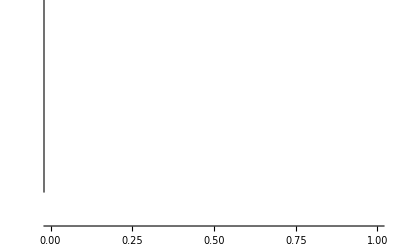

```mathematica
in1=.;in2=.;
in2=Sqrt[1-in1^2];
Plot[Simplify/@Total/@Transpose[QRWHistorgramPositionProbabilities[SparseArray[
{{8,1}->0,
{1,1}->in1,
{2,1}->in2}
],
7]],{in1,0,1}]
```

```mathematica
Transpose[Last[Flatten/@QuantumRandomWalkHistory[SparseArray[
{{8,1}->0,
{1,1}->1}
],
2,0,1,0]]]
```

Transpose::nmtx: The first two levels of the one-dimensional list {1/2, 1/2, 0, 0, 1/2, -1/2, 0, 0} cannot be transposed.

Transpose[{1/2,1/2,0,0,1/2,-1/2,0,0}]

```mathematica
Take[Transpose[Results6],-5]
```

{{1/8,5/8,1/8,1/8},{1/8,5/8,1/8,1/8},{1/8,5/8,1/8,1/8},{1/8,5/8,1/8,1/8},{1/8,1/8,5/8,1/8}}

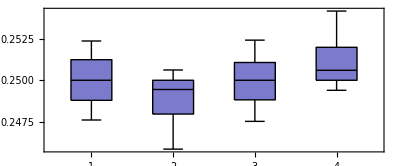
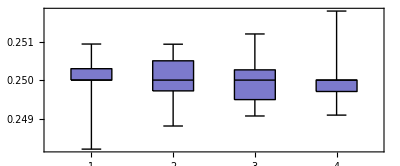
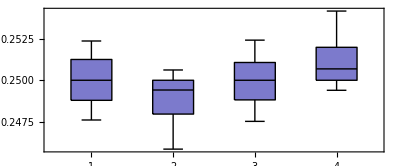

```mathematica
Table[BoxWhiskerPlot[Transpose[(Take[#,-100])&/@CumulativeMean[Transpose[Take[Transpose[v],-500]]]]],{v,{Results4,Results5,Results6}}]
Take[Transpose[Results6],-93];
```

```mathematica
Needs["StatisticalPlots`"]
Results={Results1,Results2,Results3}
Table[BoxWhiskerPlot[N[(Take[#,-500])&/@Map[Transpose,Results]][[v]]],{v,Range[3]}];
```

{{«1»},{«1»},«1»}

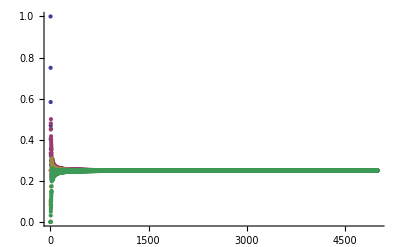
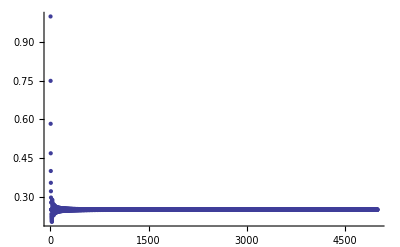
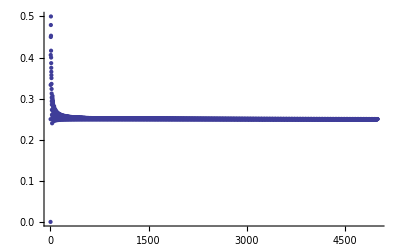
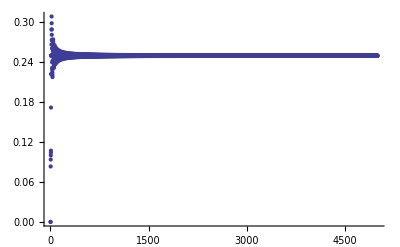
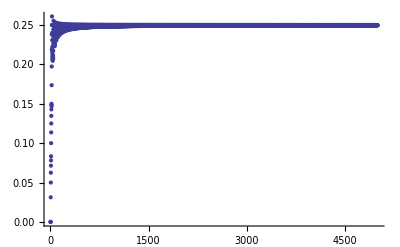
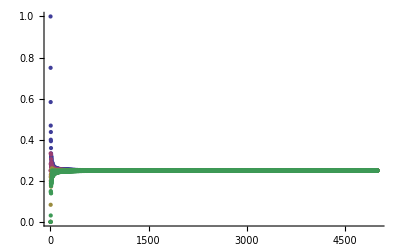
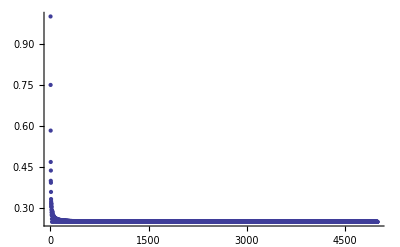
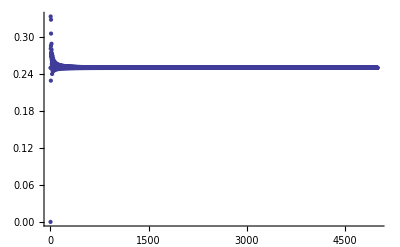

```mathematica
Table[ListPlot[v],{v,{Results1,Results1[[1]],Results1[[2]],Results1[[3]],Results1[[4]],Results2,Results2[[1]],Results2[[2]],Results2[[3]],Results2[[4]],Results3,Results3[[1]],Results3[[2]],Results3[[3]],Results3[[4]]}}]
```

```mathematica
y
```

(√(1-x^2))/(√2)

```mathematica
Simplify[x^2+2*y^2]
```

1